```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mike/Documents/Helpful_Objects/IDL/chaffin/IDL-Colorbars/colorbar_csv_source

```mathematica
cmap1=Import["matplotlib_option_d.csv","Data"];
```

```mathematica
crainbow=Import["cubehelix_rainbow_256.csv","Data"]/255.;
```

```mathematica
mplrainbow=Import["MPL_rainbow_BW.csv","Data"];
```

```mathematica
Length@crainbow
```

256

```mathematica
?Rectangle
```

RowBox[{"Rectangle", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] represents an axis-aligned filled rectangle from RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]]}], "}"}] to RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}].
RowBox[{"Rectangle", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]]}], "}"}], "]"}] corresponds to a unit square with its bottom-left corner at RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]]}], "}"}].

```mathematica
colorbar[cmap_]:=Graphics[Table[{RGBColor@@cmap[[ii]],Rectangle[{(ii-1)/Length[cmap],0},{ii/Length[cmap],1}]},{ii,1,Length[cmap]}],AspectRatio->0.2]
```

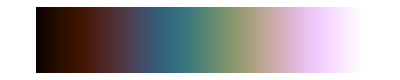

```mathematica
colorbar[crainbow]
```

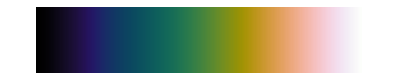

```mathematica
colorbar[mplrainbow]
```

```mathematica
idlcolorbardir="../IDL_rgb_values"
idlcolorbarnames=FileNames[idlcolorbardir<>"/*"];
SortBy[idlcolorbarnames,""];
idlcolorbars=Import[#,"CSV"]&/@idlcolorbarnames/255.;
```

../IDL_rgb_values

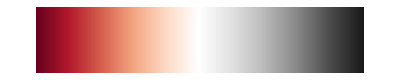

```mathematica
colorbar[idlcolorbars[[-10]]]
```

## Now write the python code for viscm

```mathematica
top="from matplotlib.colors import LinearSegmentedColormap
from numpy import nan, inf
";
```

```mathematica
bottom="

test_cm = LinearSegmentedColormap.from_list(__file__, cm_data)


if __name__ == \"__main__\":
    import matplotlib.pyplot as plt
    import numpy as np

    try:
        from pycam02ucs.cm.viscm import viscm
        viscm(test_cm)
    except ImportError:
        print(\"pycam02ucs not found, falling back on simple display\")
        plt.imshow(np.linspace(0, 100, 256)[None, :], aspect='auto',
                   cmap=test_cm)
    plt.show()
";
```

```mathematica
midstrings="cm_data = "<>StringReplace[ToString[#],{"}, {"->"],\n[","{{"->"[[","}}"->"]]"}]&/@idlcolorbars;
```

```mathematica
pyscripts=top<>#<>bottom&/@midstrings;
```

```mathematica
pytestdir="IDL_py_test/";
```

```mathematica
pyscriptname=pytestdir<>#<>".py"&/@FileBaseName/@idlcolorbarnames
```

{/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/00_B-W_LINEAR.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/01_BLUE-WHITE.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/02_GRN-RED-BLU-WHT.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/03_RED_TEMPERATURE.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/04_BLUE-GREEN-RED-YELLOW.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/05_STD_GAMMA-II.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/06_PRISM.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/07_RED-PURPLE.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/08_GREEN-WHITE_LINEAR.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/09_GRN-WHT_EXPONENTIAL.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/10_GREEN-PINK.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/11_BLUE-RED.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/12_16_LEVEL.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/13_RAINBOW.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/14_STEPS.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/15_STERN_SPECIAL.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/16_Haze.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/17_Blue_-_Pastel_-_Red.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/18_Pastels.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/19_Hue_Sat_Lightness_1.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/20_Hue_Sat_Lightness_2.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/21_Hue_Sat_Value_1.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/22_Hue_Sat_Value_2.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/23_Purple-Red_plus_Stripes.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/24_Beach.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/25_Mac_Style.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/26_Eos_A.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/27_Eos_B.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/28_Hardcandy.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/29_Nature.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/30_Ocean.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/31_Peppermint.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/32_Plasma.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/33_Blue-Red.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/34_Rainbow.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/35_Blue_Waves.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/36_Volcano.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/37_Waves.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/38_Rainbow18.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/39_Rainbow_plus_white.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/40_Rainbow_plus_black.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/41_CB-Accent.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/42_CB-Dark2.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/43_CB-Paired.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/44_CB-Pastel1.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/45_CB-Pastel2.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/46_CB-Set1.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/47_CB-Set2.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/48_CB-Set3.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/49_CB-Blues.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/50_CB-BuGn.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/51_CB-BuPu.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/52_CB-GnBu.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/53_CB-Greens.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/54_CB-Greys.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/55_CB-Oranges.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/56_CB-OrRd.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/57_CB-PuBu.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/58_CB-PuBuGn.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/59_CB-PuRd.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/60_CB-Purples.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/61_CB-RdPu.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/62_CB-Reds.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/63_CB-YlGn.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/64_CB-YlGnBu.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/65_CB-YlOrBr.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/66_CB-BrBG.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/67_CB-PiYG.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/68_CB-PRGn.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/69_CB-PuOr.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/70_CB-RdBu.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/71_CB-RdGy.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/72_CB-RdYlBu.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/73_CB-RdYlGn.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/74_CB-Spectral.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/75_LAB_rainbow.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/76_MPL_rainbow.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/77_MPL_option_A.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/78_MPL_option_B.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/79_MPL_option_C.py,/home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/80_MPL_option_D.py}

```mathematica
Do[Export[pyscriptname[[ii]],pyscripts[[ii]],"Text"],{ii,1,Length[pyscripts]}]
```

## Now run the python script to generate pngs for these colormaps

```mathematica
idlpngdir="IDL_py_png/"
```

IDL_py_png/

```mathematica
pypngcmds=
Table["python -m viscm show "<>pyscriptname[[ii]]<>" --save "<>idlpngdir<>FileBaseName[idlcolorbarnames[[ii]]]<>".png"<>" --quit",{ii,1,idlcolorbarnames//Length}];
```

```mathematica
?RunProcess
```

RunProcess["command"] runs the specified external command, returning information on the outcome.
RunProcess[{"command", arg 1, arg 2, …}] runs the specified command, with command-line arguments arg i.
RunProcess[command, "prop"] returns only the specified property.
RunProcess[command, prop, input] feeds the specified initial input to the command.

```mathematica
pypngcmds[[1]]
```

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/00_B-W_LINEAR.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/00_B-W_LINEAR.png --quit

```mathematica
bashproc=StartProcess["/bin/bash"]
```

ProcessObject[4]

```mathematica
pypngcmds[[1]]
```

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/00_B-W_LINEAR.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/00_B-W_LINEAR.png --quit

```mathematica
StringJoin[Riffle[pypngcmds,"\n\n"]]
```

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/00_B-W_LINEAR.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/00_B-W_LINEAR.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/01_BLUE-WHITE.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/01_BLUE-WHITE.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/02_GRN-RED-BLU-WHT.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/02_GRN-RED-BLU-WHT.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/03_RED_TEMPERATURE.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/03_RED_TEMPERATURE.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/04_BLUE-GREEN-RED-YELLOW.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/04_BLUE-GREEN-RED-YELLOW.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/05_STD_GAMMA-II.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/05_STD_GAMMA-II.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/06_PRISM.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/06_PRISM.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/07_RED-PURPLE.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/07_RED-PURPLE.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/08_GREEN-WHITE_LINEAR.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/08_GREEN-WHITE_LINEAR.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/09_GRN-WHT_EXPONENTIAL.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/09_GRN-WHT_EXPONENTIAL.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/10_GREEN-PINK.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/10_GREEN-PINK.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/11_BLUE-RED.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/11_BLUE-RED.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/12_16_LEVEL.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/12_16_LEVEL.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/13_RAINBOW.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/13_RAINBOW.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/14_STEPS.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/14_STEPS.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/15_STERN_SPECIAL.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/15_STERN_SPECIAL.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/16_Haze.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/16_Haze.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/17_Blue_-_Pastel_-_Red.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/17_Blue_-_Pastel_-_Red.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/18_Pastels.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/18_Pastels.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/19_Hue_Sat_Lightness_1.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/19_Hue_Sat_Lightness_1.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/20_Hue_Sat_Lightness_2.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/20_Hue_Sat_Lightness_2.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/21_Hue_Sat_Value_1.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/21_Hue_Sat_Value_1.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/22_Hue_Sat_Value_2.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/22_Hue_Sat_Value_2.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/23_Purple-Red_plus_Stripes.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/23_Purple-Red_plus_Stripes.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/24_Beach.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/24_Beach.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/25_Mac_Style.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/25_Mac_Style.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/26_Eos_A.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/26_Eos_A.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/27_Eos_B.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/27_Eos_B.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/28_Hardcandy.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/28_Hardcandy.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/29_Nature.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/29_Nature.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/30_Ocean.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/30_Ocean.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/31_Peppermint.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/31_Peppermint.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/32_Plasma.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/32_Plasma.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/33_Blue-Red.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/33_Blue-Red.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/34_Rainbow.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/34_Rainbow.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/35_Blue_Waves.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/35_Blue_Waves.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/36_Volcano.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/36_Volcano.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/37_Waves.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/37_Waves.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/38_Rainbow18.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/38_Rainbow18.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/39_Rainbow_plus_white.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/39_Rainbow_plus_white.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/40_Rainbow_plus_black.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/40_Rainbow_plus_black.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/41_CB-Accent.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/41_CB-Accent.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/42_CB-Dark2.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/42_CB-Dark2.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/43_CB-Paired.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/43_CB-Paired.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/44_CB-Pastel1.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/44_CB-Pastel1.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/45_CB-Pastel2.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/45_CB-Pastel2.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/46_CB-Set1.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/46_CB-Set1.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/47_CB-Set2.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/47_CB-Set2.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/48_CB-Set3.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/48_CB-Set3.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/49_CB-Blues.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/49_CB-Blues.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/50_CB-BuGn.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/50_CB-BuGn.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/51_CB-BuPu.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/51_CB-BuPu.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/52_CB-GnBu.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/52_CB-GnBu.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/53_CB-Greens.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/53_CB-Greens.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/54_CB-Greys.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/54_CB-Greys.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/55_CB-Oranges.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/55_CB-Oranges.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/56_CB-OrRd.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/56_CB-OrRd.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/57_CB-PuBu.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/57_CB-PuBu.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/58_CB-PuBuGn.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/58_CB-PuBuGn.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/59_CB-PuRd.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/59_CB-PuRd.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/60_CB-Purples.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/60_CB-Purples.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/61_CB-RdPu.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/61_CB-RdPu.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/62_CB-Reds.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/62_CB-Reds.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/63_CB-YlGn.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/63_CB-YlGn.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/64_CB-YlGnBu.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/64_CB-YlGnBu.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/65_CB-YlOrBr.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/65_CB-YlOrBr.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/66_CB-BrBG.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/66_CB-BrBG.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/67_CB-PiYG.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/67_CB-PiYG.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/68_CB-PRGn.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/68_CB-PRGn.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/69_CB-PuOr.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/69_CB-PuOr.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/70_CB-RdBu.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/70_CB-RdBu.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/71_CB-RdGy.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/71_CB-RdGy.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/72_CB-RdYlBu.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/72_CB-RdYlBu.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/73_CB-RdYlGn.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/73_CB-RdYlGn.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/74_CB-Spectral.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/74_CB-Spectral.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/75_LAB_rainbow.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/75_LAB_rainbow.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/76_MPL_rainbow.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/76_MPL_rainbow.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/77_MPL_option_A.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/77_MPL_option_A.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/78_MPL_option_B.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/78_MPL_option_B.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/79_MPL_option_C.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/79_MPL_option_C.png --quit

python -m viscm show /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_test/80_MPL_option_D.py --save /home/mike/Documents/Helpful_Objects/IDL/chaffin/colorbars/IDL_py_png/80_MPL_option_D.png --quit

I then copied and pasted the above expression into a terminal, which had the desired effect.